```mathematica
Subsets[Range[9],{5}]//Length
```

126

```mathematica
Avoiding[length_]:=Block[{all=Subsets[Range[length],{5}],sample,nodes,result={}},
While[all≠{},
sample=RandomChoice[all];
nodes=Sort[RandomSample[sample,2]];
AppendTo[result,UndirectedEdge[nodes[[1]],nodes[[2]]]];
all=Select[all,Sort[Intersection[#,nodes]]≠nodes&];
];
result
]
```

```mathematica
With[{max=6},ChromaticPolynomial[EdgeDelete[CompleteGraph[max],Avoiding[max]],4]]
```

24

```mathematica
Monitor[Table[ChromaticPolynomial[EdgeDelete[CompleteGraph[max],Avoiding[max]],4],{max,10,13}],max]
```

{24,24,24,24,24,24,0,0,0}

```mathematica
Table[With[{edges=Avoiding[max]},With[{g=CompleteGraph[max,GraphHighlight->edges,GraphHighlightStyle->"Thick"]},Labeled[g,{ChromaticPolynomial[g,4],Length[edges],Binomial[max,2]-(3*max-6)}]]],{max,10,13}]
```

{-Graphics-{0,13,21},-Graphics-{0,20,28},-Graphics-{0,21,36},-Graphics-{0,30,45}}

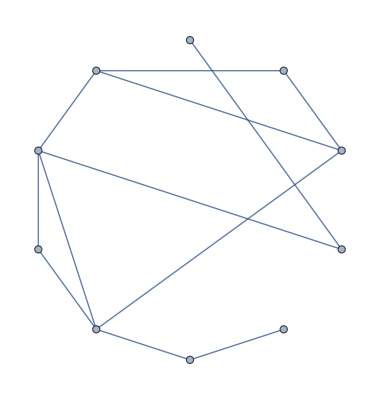
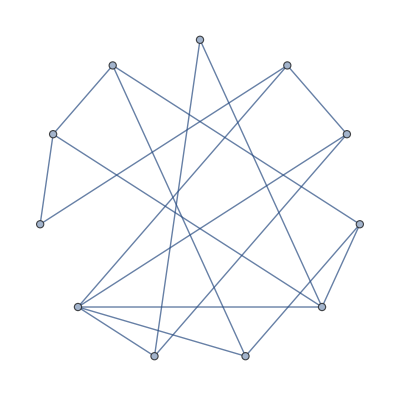
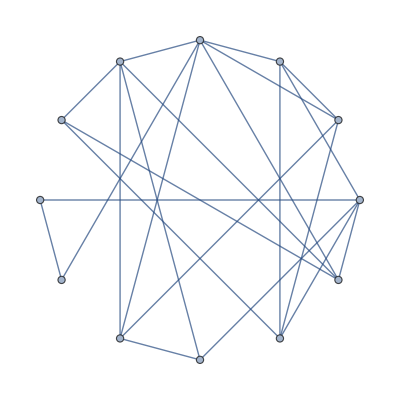
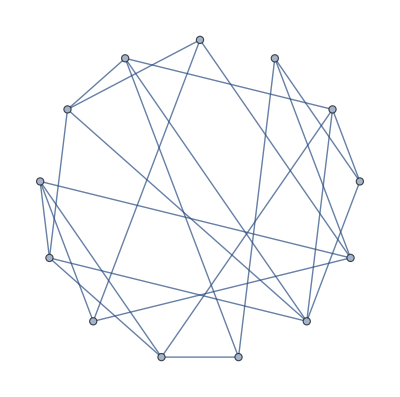
{-Graphics-{24,{{5,6,9}},12,21},-Graphics-{0,{{4,11,10}},17,28},-Graphics-{0,{{7,8,2}},23,36},-Graphics-{0,{{1,5,12}},24,45}}

```mathematica
Table[With[{edges=Avoiding[max]},With[{g=Graph[edges,GraphLayout->"CircularEmbedding"]},Labeled[g,{ChromaticPolynomial[EdgeDelete[CompleteGraph[max],edges],4],FindClique[g],Length[edges],Binomial[max,2]-(3*max-6)}]]],{max,10,13}]
```

```mathematica
Monitor[Table[{Binomial[max,2]-(3*max-6),Length[Avoiding[max]]},{max,5,13}],max]
```

{{1,1},{3,1},{6,1},{10,1},{15,1},{21,1},{28,1},{36,1},{45,1}}

```mathematica
SmartTake[list_,l_]:=If[Length[list]<l,list,Take[list,l]]
```

```mathematica
AvoidingComplete[length_,max_]:=Block[{all=Subsets[Range[length],{5}]},
Map[Last,Select[Flatten[AvoidingComplete[max,all,{}]],#=!=Null&]]
]
```

```mathematica
AvoidingComplete[max_,all_,result_]:=Block[{localresult,localall,localresults={},temp},
If[all=={},
Print[result];
1->result,
Table[
localresults=Table[
localresult=Append[result,UndirectedEdge[edge[[1]],edge[[2]]]];
localall=Select[all,Sort[Intersection[#,edge]]≠edge&];
{localresult,localall}
,
{edge,Subsets[tuple,{2}]}
];
,
{tuple,all}
];

localresults=Select[localresults,Length[#[[1]]]<=max&];
temp=Tally[localresults,IsomorphicGraphQ[Graph[#1[[1]]],Graph[#2[[1]]]]&];
localresults=Map[First,temp];
Monitor[
Table[
localall=var[[2]];
localresult=var[[1]];
AvoidingComplete[max,localall,localresult]
,{var,SmartTake[localresults,2]}

],
{Length[all],localresult}]
]
]
```

```mathematica
Tally[AvoidingComplete[6,3],Length[#1]==Length[#2]&]
```

{{{1<->2,1<->3,2<->3},36},{{1<->2,3<->4},12}}

```mathematica
Monitor[Table[Print[Sort[Map[Length[First[#]]&,Tally[AvoidingComplete[k,21],Length[#1]==Length[#2]&]]]],{k,5,10}],k]
```

{1}

{2,3}

{3,4,5,6}

{4,5,6,7,8,9,10}

{6,7,8,9,10,11,12,13,14,15}

{8,9,10,11,12,13,14,15,16,17,18,19,20,21}

{Null,Null,Null,Null,Null,Null}

```mathematica
Monitor[Table[Print[Sort[Map[Length[First[#]]&,Tally[AvoidingComplete[k,21],Length[#1]==Length[#2]&]]]],{k,11,12}],k]
```

```mathematica
Monitor[Table[Print[Tally[AvoidingComplete[k,21],Length[#1]==Length[#2]&]],{k,5,10}],k]
```

{{{1<->2},1}}

{{{2<->3,1<->3,1<->2},3},{{2<->3,1<->4},1}}

{{{3<->4,2<->4,2<->3,1<->4,1<->3,1<->2},44},{{3<->4,2<->4,2<->3,1<->4,1<->5},38},{{3<->4,2<->4,2<->3,1<->5},9},{{3<->4,2<->5,1<->6},1}}

{{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->4,1<->3,1<->2},4409},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->4,1<->6},9799},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6},6307},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},1328},{{4<->5,3<->5,3<->4,2<->5,2<->6,1<->7},163},{{4<->5,3<->5,3<->4,2<->6,1<->7},14},{{4<->5,3<->6,2<->7,1<->8},1}}

$Aborted

```mathematica
Sort[Tally[AvoidingComplete[10,20],Length[#1]==Length[#2]&],Length[#1]<Length[#2]&]
```

{{{6<->7,5<->8,4<->9,3<->10,2<->7,2<->6,1<->8,1<->5},1},{{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->9,1<->2},10},{{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->7,1<->6,1<->5},31},{{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->7,2<->8,2<->9,1<->9,1<->2},79},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->8,2<->8,2<->3,1<->8,1<->3,1<->2},167},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->8,1<->8,1<->2},429},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->8,1<->8,1<->2},781},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->8,1<->8,1<->2},2168},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->8},5698},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->8},9642},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->8},8625},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->8},3524},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->4,1<->8},628}}

```mathematica
AvoidingComplete[10,20]
```

{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->4,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->8},31775,{6<->7,5<->8,4<->9,3<->10,7<->8,2<->8,2<->7,2<->9,2<->5,1<->8,1<->5,1<->4},{6<->7,5<->8,4<->9,3<->10,7<->8,2<->8,2<->7,2<->9,2<->5,1<->8,1<->7,1<->5,1<->2},{6<->7,5<->8,4<->9,3<->10,7<->8,2<->8,2<->7,2<->9,2<->5,1<->8,1<->7,1<->5,1<->4},{6<->7,5<->8,4<->9,3<->10,7<->8,2<->8,2<->7,2<->9,2<->5,1<->8,1<->7,1<->6}}
 |  |  |  |

```mathematica
Table[Print[Tally[AvoidingComplete[k,21],Length[#1]==Length[#2]&]],{k,5,10}]
```

{{{1<->2},1}}

{{{1<->2,1<->3,2<->3},36},{{1<->2,3<->4},12}}

{{{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4},303072},{{1<->2,1<->3,1<->4,2<->3,4<->5},146832},{{1<->2,1<->3,4<->5,2<->3},23436},{{1<->2,3<->4,5<->6},924}}

```mathematica
Tally[AvoidingComplete[8,3],Length[#1]==Length[#2]&]
```

```mathematica
SelectFirst[AvoidingComplete[7,6],Length[#]==6&]
```

{1<->2,1<->3,2<->3}

```mathematica
With[{g=Graph[{1<->2,1<->3,4<->5,2<->3}]},Labeled[CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[GraphComplement[g]],GraphHighlightStyle->"Thick"],{3VertexCount[g]-6,EdgeCount[g]}]]
```

-Graphics-{9,4}

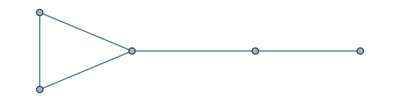
-Graphics-{{1,2,3}}

```mathematica
With[{g=Graph[{1<->2,1<->3,1<->4,2<->3,4<->5}]},Labeled[g,FindClique[g]]]
```

```mathematica
Map[Length,AvoidingComplete[6,2]]//Tally//Sort
```

{{2,6}}

```mathematica
Map[Length,AvoidingComplete[7,3]]//Tally//Sort
```

{{3,176400}}

```mathematica
Map[Length,AvoidingComplete[9,6]]//Tally//Sort
```

$Aborted

```mathematica
Map[Length,AvoidingComplete[10,7]]//Tally//Sort
```

$Aborted

```mathematica
Map[Length,AvoidingComplete[5]]//Tally//Sort
```

{{1,3}}

```mathematica
Map[Length,AvoidingComplete[6]]//Tally//Sort
```

{{2,4},{3,15}}

```mathematica
Map[Length,AvoidingComplete[7]]//Tally//Sort
```

{{3,7},{4,30},{5,78},{6,36}}

```mathematica
Map[Length,AvoidingComplete[8]]//Tally//Sort
```

{{4,3},{5,22},{6,174},{7,762},{8,1411},{9,1266},{10,351}}

```mathematica
Map[Length,AvoidingComplete[9]]//Tally//Sort
```

{{6,3},{7,68},{8,659},{9,4218},{10,17313},{11,39949},{12,54146},{13,41187},{14,16592},{15,2226}}

```mathematica
Map[Length,AvoidingComplete[10]]//Tally//Sort
```

{{9,45},{10,636},{11,6809},{12,53458},{13,298854},{14,1155345},{15,3075269},{16,5631953},{17,7103603},{18,6047109},{19,3293742},{20,1030711},{21,138525}}

```mathematica
Map[Length,AvoidingComplete[11]]//Tally//Sort
```

```mathematica
Map[Length,AvoidingComplete[11]]//Tally//Sort
```

$Aborted

```mathematica
Sort[Tally[AvoidingComplete[8,8],IsomorphicGraphQ[Graph[#1],Graph[#2]]&],Length[#1]<Length[#2]&]
```

{{{4<->5,3<->6,2<->7,1<->8},1},{{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},1},{{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},1},{{4<->5,3<->6,2<->7,1<->5,1<->4},1},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},1},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},2},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},1},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},1},{{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},1},{{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},1},{{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},2},{{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},7},{{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},8},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},8},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},10},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},3},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6},11}}

```mathematica
Sort[Tally[AvoidingComplete[12,12],IsomorphicGraphQ[Graph[#1],Graph[#2]]&],Length[#1]<Length[#2]&]
```

{{{8<->9,7<->9,7<->8,6<->10,5<->10,5<->6,4<->11,3<->11,3<->4,2<->12,1<->12,1<->2},4}}

```mathematica
Sort[Tally[AvoidingComplete[13,15],IsomorphicGraphQ[Graph[#1],Graph[#2]]&],Length[#1]<Length[#2]&]
```

{9<->10,8<->10,8<->9,7<->11,6<->11,6<->7,5<->12,4<->12,4<->5,3<->13,2<->13,2<->3,1<->10,1<->9,1<->8}

$Aborted

{{Last[$Aborted],1}}

```mathematica
Sort[Tally[AvoidingComplete[14,18],IsomorphicGraphQ[Graph[#1],Graph[#2]]&],Length[#1]<Length[#2]&]
```

$Aborted

{{Last[$Aborted],1}}